```mathematica
(* Линейни системи *)
{x,x^2,y,z}/.x->2
```

{2,4,y,z}

```mathematica
s=Solve[3 x-5==0,x]
```

{{x→5/3}}

```mathematica
s^2
```

{{(x→5/3)^2}}

```mathematica
sol=x/.Solve[3 x-5==0,x]
```

{5/3}

```mathematica
Head[sol]
```

List

```mathematica
z=First[sol]
```

5/3

```mathematica
z^2
```

25/9

```mathematica
Solve[3 Abs[x]-5==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-5/3},{x→5/3}}

```mathematica
sol=x/.Solve[3 Abs[x]-5==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-5/3,5/3}

```mathematica
Head[sol]
```

List

```mathematica
Solve[3 Abs[x]-5==0&&x∈Reals,x]
```

{{x→-5/3},{x→5/3}}

```mathematica
sol=x/.Solve[3 Abs[x]-5==0,x,Reals]
```

{-5/3,5/3}

```mathematica
(*  ({{2, -7}, {-1, 4}})({{x}, {y}})=({{1}, {7}})*)
s=Solve[{2 x-7==1,-x+4 y==7},{x,y}]
```

{{x→4,y→11/4}}

```mathematica
sol={x,y}/.s
```

{{4,11/4}}

```mathematica
x0=First[Flatten[sol]]
```

4

```mathematica
y0=Last[Flatten[sol]]
```

11/4

```mathematica
LinearSolve[{{2,-7},{-1,4}},{1,7}]
```

{53,15}

```mathematica
Clear[a,b,x0,y0]
```

```mathematica
a=({{2, -7}, {-1, 4}});
b=({{1}, {7}});
```

```mathematica
ls=LinearSolve[a,b]
```

{{53},{15}}

```mathematica
First[ls]
```

{53}

```mathematica
x0=Flatten[ls][[1]]
```

53

```mathematica
y0=Part[Flatten[ls],2]
```

15

```mathematica
Clear[a,b]
```

```mathematica
a=({{2, 1, 0}, {-1, 3, 5}, {4, 0, -2}});
b=({{3}, {-21}, {6}});
```

```mathematica
MatrixRank[a]
```

3

```mathematica
LinearSolve[a,b]
```

{{-5},{13},{-13}}

```mathematica
Clear[a,b]
```

```mathematica
a=({{2, 1, 0, -7}, {-1, 3, 5, 4}, {4, 0, -2, 3}});
b=({{3}, {-21}, {6}});
```

```mathematica
MatrixRank[a]
```

3

```mathematica
LinearSolve[a,b]
```

{{-5},{13},{-13},{0}}

```mathematica
Clear[a,b]
```

```mathematica
a=({{2, 1, 0, -7}, {-1, 3, 5, 4}, {4, 0, -2, 3}});
b=({{3, -12}, {-21, 6}, {6, 18}});
```

```mathematica
LinearSolve[a,b]//MatrixForm
```

(-5 | 29
13 | -70
-13 | 49
0 | 0)

```mathematica
Clear[u,v,w,t]
```

```mathematica
Solve[{2 u+v-7 t==1,-u+3 v+5 w+4 t==-7,4 u-2 w+3 t==2},{u,v,w}]
```

{{u→-5/6 (2+13 t),v→1/3 (13+86 t),w→1/6 (-26-121 t)}}

```mathematica
MatrixRank[({{2, 1, 0, -7}, {-1, 3, 5, 4}, {4, 0, -2, 3}})]
```

3

```mathematica
Clear[a,x,y,z]
```

```mathematica
Eliminate[{a x+y==0,2 x+(a-1) y+z==1,5 x+a y-2 z==0},{y,z}]
```

(-9-2 a+3 a^2) x==-2

```mathematica
Solve[{a x+y==0,2 x+(a-1) y+z==1,5 x+a y-2 z==0},{x,y,z}]
```

{{x→-2/(-9-2 a+3 a^2),y→(2 a)/(-9-2 a+3 a^2),z→-(5-a^2)/(-9-2 a+3 a^2)}}

```mathematica
Clear[a,x]
```

```mathematica
Solve[{x==1,x==a},x]
```

{}

```mathematica
Reduce[{x==1,x==a,x}]
```

Reduce::naqs: x==1&&x==a&&x is not a quantified system of equations and inequalities.

Reduce[{x==1,x==a,x}]

```mathematica
Clear[a,b,x]
```

```mathematica
Reduce[{a x+b==0},x]
```

(b==0&&a==0)||(a≠0&&x==-b/a)

```mathematica
Clear[a,b,x]
```

```mathematica
Reduce[{(x+a)/(x-1)+x/(2 a)==3},x]
```

(x==1/2 (1+4 a-√(1-16 a+8 a^2))||x==1/2 (1+4 a+√(1-16 a+8 a^2)))&&-a+a x≠0

```mathematica
Clear[a,b,x,y]
```

```mathematica
Solve[{a x+b y==1,x-y==2},{x,y}]
```

{{x→-(-1-2 b)/(a+b),y→-(-1+2 a)/(a+b)}}

```mathematica
n=5;
a=SparseArray[{Band[{1,1}]->3,Band[{2,1}]->1,Band[{1,2}]->-2},{n,n}];
b=Table[RandomInteger[{-5,5}],n];
Print["a=",MatrixForm[a],"  b=",MatrixForm[b]]
LinearSolve[a,b]//MatrixForm
```

a=(3 | -2 | 0 | 0 | 0
1 | 3 | -2 | 0 | 0
0 | 1 | 3 | -2 | 0
0 | 0 | 1 | 3 | -2
0 | 0 | 0 | 1 | 3)  b=(1
3
1
1
5)

(521/495
178/165
29/45
166/165
659/495)

```mathematica
(* Алгебрични уравнения *)
Solve[x^2+4 x-5==0,x]
```

{{x→-5},{x→1}}

```mathematica
Clear[a,b,x]
```

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Clear[a,b,x]
```

```mathematica
Reduce[a x^2+b x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

```mathematica
Clear[p,x]
```

```mathematica
Solve[2 x-4(p x-1)-2 p^2+p-3==0,x]
```

{{x→(1+p-2 p^2)/(2 (-1+2 p))}}

```mathematica
Reduce[2 x-4(p x-1)-2 p^2+p-3==0,x]
```

-1+2 p≠0&&x==(1+p-2 p^2)/(2 (-1+2 p))

```mathematica
Solve[x^3+4 x+7==0,x]//N
```

{{x→-1.25538},{x→0.627692-2.2764 ⅈ},{x→0.627692+2.2764 ⅈ}}

```mathematica
RootIntervals[x^3+4x+7]
```

{{{-2,0}},{{1}}}

```mathematica
Solve[x^4+3 x^2-4x+7==0,x]
```

{{x→Root-0.837-1.84 ⅈRoot[7-4 #1+3 #1^2+#1^4&,1]-0.8374731709694437},{x→Root-0.837+1.84 ⅈRoot[7-4 #1+3 #1^2+#1^4&,2]-0.8374731709694437},{x→Root0.837-1.00 ⅈRoot[7-4 #1+3 #1^2+#1^4&,3]0.8374731709694438},{x→Root0.837+1.00 ⅈRoot[7-4 #1+3 #1^2+#1^4&,4]0.8374731709694438}}

```mathematica
Solve[x^6-x^5+3 x^2-4 x+7==0,x]
```

{{x→Root-1.15-0.928 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,1]-1.1491672527078336},{x→Root-1.15+0.928 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,2]-1.1491672527078336},{x→Root0.323-1.14 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,3]0.32342828973801124},{x→Root0.323+1.14 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,4]0.32342828973801124},{x→Root1.33-0.717 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,5]1.3257389629698224},{x→Root1.33+0.717 ⅈRoot[7-4 #1+3 #1^2-#1^5+#1^6&,6]1.3257389629698224}}

```mathematica
NRoots[x^6-x^5+3 x^2-4 x+7==0,x]
```

x==-1.14917-0.927705 ⅈ||x==-1.14917+0.927705 ⅈ||x==0.323428-1.14376 ⅈ||x==0.323428+1.14376 ⅈ||x==1.32574-0.716903 ⅈ||x==1.32574+0.716903 ⅈ

```mathematica
Solve[x^13-x^9+3 x^7-x^6-x^5+3 x^2-4 x+7==0,x]//N
```

{{x→-1.19488},{x→-1.15076-0.615743 ⅈ},{x→-1.15076+0.615743 ⅈ},{x→-0.553615-0.922295 ⅈ},{x→-0.553615+0.922295 ⅈ},{x→-0.0323416-1.35357 ⅈ},{x→-0.0323416+1.35357 ⅈ},{x→0.329047-0.912065 ⅈ},{x→0.329047+0.912065 ⅈ},{x→0.895374-0.709353 ⅈ},{x→0.895374+0.709353 ⅈ},{x→1.10973-0.300263 ⅈ},{x→1.10973+0.300263 ⅈ}}

```mathematica
NSolve[2 x^13+x^12-11 x^11+17 x^10+4 x^9-29 x^8+14 x^7+5 x^6+3 x^5+x^4-22 x^3+62 x^2-68 x+21==0,x,Reals]
```

{{x→-3.},{x→0.5},{x→1.}}

```mathematica
NSolve[2 x^13+x^12-11 x^11+17 x^10+4 x^9-29 x^8+14 x^7+5 x^6+3 x^5+x^4-22 x^3+62 x^2-68 x+21==0&&Abs[x]≤1.1,x]
```

{{x→-0.55729-0.929249 ⅈ},{x→-0.55729+0.929249 ⅈ},{x→0.315561-0.963872 ⅈ},{x→0.315561+0.963872 ⅈ},{x→0.5},{x→1.}}

```mathematica
NSolve[2 x^13+x^12-11 x^11+17 x^10+4 x^9-29 x^8+14 x^7+5 x^6+3 x^5+x^4-22 x^3+62 x^2-68 x+21==0&&0.9≤Abs[x]≤1.1,x]
```

{{x→-0.55729-0.929249 ⅈ},{x→-0.55729+0.929249 ⅈ},{x→0.315561-0.963872 ⅈ},{x→0.315561+0.963872 ⅈ},{x→1.}}

```mathematica
CountRoots[2 x^13+x^12-11 x^11+17 x^10+4 x^9-29 x^8+14 x^7+5 x^6+3 x^5+x^4-22 x^3+62 x^2-68 x+21,x]
```

3

```mathematica
CountRoots[2 x^13+x^12-11 x^11+17 x^10+4 x^9-29 x^8+14 x^7+5 x^6+3 x^5+x^4-22 x^3+62 x^2-68 x+21,{x,-1,2}]
```

2

```mathematica
(* Диофантови уравнения *)
Solve[x^2+y^2==25,{x,y},Integers]
```

{{x→-5,y→0},{x→-4,y→-3},{x→-4,y→3},{x→-3,y→-4},{x→-3,y→4},{x→0,y→-5},{x→0,y→5},{x→3,y→-4},{x→3,y→4},{x→4,y→-3},{x→4,y→3},{x→5,y→0}}

```mathematica
Length[%]
```

12

```mathematica
Solve[x^2+y^2==25&&x>-1,{x,y},Integers]
```

{{x→0,y→-5},{x→0,y→5},{x→3,y→-4},{x→3,y→4},{x→4,y→-3},{x→4,y→3},{x→5,y→0}}

```mathematica
Clear[x,y]
```

```mathematica
Solve[x^2+y^2==3681&&x>0&&y>0,{x,y},Integers]
```

{{x→9,y→60},{x→60,y→9}}

```mathematica
(* Нелинейни уравнения *)
Solve[ArcSin[x]==a,x]
```

{{x→ConditionalExpression[Sin[a],(Re[a]==-π/2&&Im[a]≥0)||-π/2<Re[a]<π/2||(Re[a]==π/2&&Im[a]≤0)]}}

```mathematica
Reduce[Sin[x]==a,x]
```

C[1]∈ℤ&&(x==π-ArcSin[a]+2 π C[1]||x==ArcSin[a]+2 π C[1])

```mathematica
NSolve[3 x^2-2 ArcSin[x]-1==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-1+3 x^2-2 ArcSin[x]==0,x]

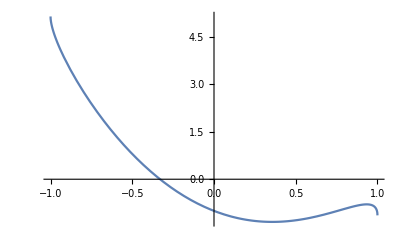

```mathematica
Plot[3 x^2-2 ArcSin[x]-1==0,{x,-1,1}]
```

```mathematica
FindRoot[3 x^2-2 ArcSin[x]-1==0,{x,0}]
```

{x→-0.330169}

```mathematica
f[x_]:=ⅇ^x-x^3+2 x+Sin[x]-3
```

```mathematica
FindRoot[f[x]==0,{x,0}]
```

{x→0.499167}

```mathematica
FindRoot[f[x]==0,{x,3}]
```

{x→2.33297}

```mathematica
FindRoot[f[x]==0,{x,5}]
```

{x→4.3531}

```mathematica
CountRoots[f[x],{x,-1,5}]
```

3

```mathematica
(* Нелинейни системи *)
Solve[{x^2+y^2==1,x+3 y==0},{x,y}]
```

{{x→-3/(√10),y→1/(√10)},{x→3/(√10),y→-1/(√10)}}

```mathematica
s=N[Solve[{x^2+y^2==1,x+3 y==0},{x,y}],15];
Cos[2 x+3y-5]/.x->s
```

{{Cos[5-3 y-2 (x→-0.948683298050514)],Cos[5-3 y-2 (y→0.316227766016838)]},{Cos[5-3 y-2 (x→0.948683298050514)],Cos[5-3 y-2 (y→-0.316227766016838)]}}

```mathematica
s
```

{{x→-0.948683298050514,y→0.316227766016838},{x→0.948683298050514,y→-0.316227766016838}}

```mathematica
s=Solve[{x^2+y^2==1,x+y==a},{x,y},Reals];
{x,y}/.s
```

{{ConditionalExpression[a/2-(√(2-a^2))/2,-√2<a<√2],ConditionalExpression[a/2+(√(2-a^2))/2,-√2<a<√2]},{ConditionalExpression[a/2+(√(2-a^2))/2,-√2<a<√2],ConditionalExpression[a/2-(√(2-a^2))/2,-√2<a<√2]}}

```mathematica
Reduce[{x^2+y^2==1,x+y==a},{x,y},Reals]
```

((a==-√2&&x==-1/(√2))||(-√2<a<√2&&(x==a/2-(√(2-a^2))/2||x==a/2+(√(2-a^2))/2))||(a==√2&&x==1/(√2)))&&y==a-x

```mathematica
Solve[{x^2+y^2==1,x+y==a},{x,y}]
```

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→1/2 (a+√(2-a^2)),y→1/2 (a-√(2-a^2))}}

```mathematica
x^3+y^3/.%/.a->7/10
```

{1/8 (7/10-(√151)/10)^3+1/8 (7/10+(√151)/10)^3,1/8 (7/10-(√151)/10)^3+1/8 (7/10+(√151)/10)^3}

```mathematica
s=Solve[{x^2/9+y^2/4==1,x+y==a},{x,y},Reals];
{x,y}/.s/.a->0.3
```

{{-1.45064,1.75064},{1.86602,-1.56602}}

```mathematica
N[Solve[{x^4+y^3-2 x y==π,Cos[x]+y+x y-1==0},{x,y},Reals],10]
```

{{x→-1.862367992,y→-1.492933321},{x→-0.7494563369,y→1.069436976},{x→1.422928702,y→0.3519173453}}

```mathematica
NSolve[{x^4+y^3-2 x y==π,Cos[x]+y+x y-1==0},{x,y},Reals]
```

{{x→-1.86237,y→-1.49293},{x→-0.749456,y→1.06944},{x→1.42293,y→0.351917}}

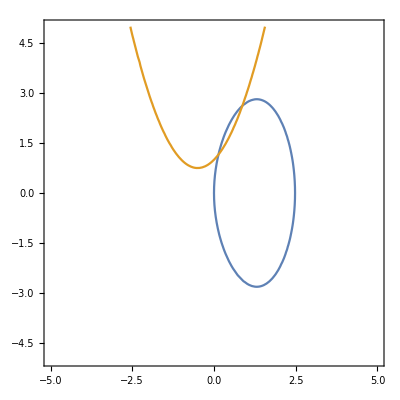

```mathematica
ContourPlot[{x^2+y^2-10 Sin[x]==0,x^2+x+1-y==0},{x,-5,5},{y,-5,5}]
```

```mathematica
FindRoot[{x^2+y^2-10 Sin[x]==0,x^2+x+1-y==0},{x,0},{y,0}]
```

{x→0.135335,y→1.15365}

```mathematica
(* --- Метод на разполовяването --- *)
f[x_]:=x^6/10+x-3
```

```mathematica
a=1;
b=2;
```

```mathematica
For[n=0,n<11,n++,Print[Subscript["a",n]," = ",NumberForm[N[a],{12,10}],"  ",Subscript["b",n]," = ",NumberForm[N[b],{12,10}],"   |",TraditionalForm[Subscript["b",n]-Subscript["a",n]],"|=",NumberForm[N[Abs[b-a]],{12,10}]];
If[f[a]f[(a+b)/2]<0,b=(a+b)/2,a=(a+b)/2]]
```

a_0 = 1.0000000000  b_0 = 2.0000000000   |b_0-a_0|=1.0000000000

a_1 = 1.5000000000  b_1 = 2.0000000000   |b_1-a_1|=0.5000000000

a_2 = 1.5000000000  b_2 = 1.7500000000   |b_2-a_2|=0.2500000000

a_3 = 1.5000000000  b_3 = 1.6250000000   |b_3-a_3|=0.1250000000

a_4 = 1.5000000000  b_4 = 1.5625000000   |b_4-a_4|=0.0625000000

a_5 = 1.5312500000  b_5 = 1.5625000000   |b_5-a_5|=0.0312500000

a_6 = 1.5468750000  b_6 = 1.5625000000   |b_6-a_6|=0.0156250000

a_7 = 1.5546875000  b_7 = 1.5625000000   |b_7-a_7|=0.0078125000

a_8 = 1.5585937500  b_8 = 1.5625000000   |b_8-a_8|=0.0039062500

a_9 = 1.5585937500  b_9 = 1.5605468750   |b_9-a_9|=0.0019531250

a_10 = 1.5595703125  b_10 = 1.5605468750   |b_10-a_10|=0.0009765625

```mathematica
(* --- Метод на Нютон --- *)
f[x_]:=x^6/10+x-3
a=1;
b=2;
```

```mathematica
If[f[a] f''[a]>0,Subscript[x, 0]=a,Subscript[x, 0]=b]
For[n=0,n<7,n++,Subscript[x, n]=Subscript[x, 0]-f[Subscript[x, 0]]/f'[Subscript[x, 0]];Print[Subscript["x",n]," = ",N[Subscript[x, n],10],"   d=",N[Abs[Subscript[x, n]-Subscript[x, 0]]]];Subscript[x, 0]=Subscript[x, n]]
```

2

x_0 = 1.732673267   d=0.

x_1 = 1.59395434   d=0.138719

x_2 = 1.561334585   d=0.0326198

x_3 = 1.559807894   d=0.00152669

x_4 = 1.559804721   d=3.17275×10^-6

x_5 = 1.559804721   d=1.36671×10^-11

x_6 = 1.559804721   d=2.53601×10^-22

```mathematica
f[x_,y_]:=x^2-4 x+y^2
g[x_,y_]:=x^2+y^2+6 x-2 y-6
NSolve[{f[x,y]==0,g[x,y]==0},{x,y},WorkingPrecision->10]
```

{{x→0.939084557,y→1.69542279},{x→0.36860775,y→-1.15696125}}

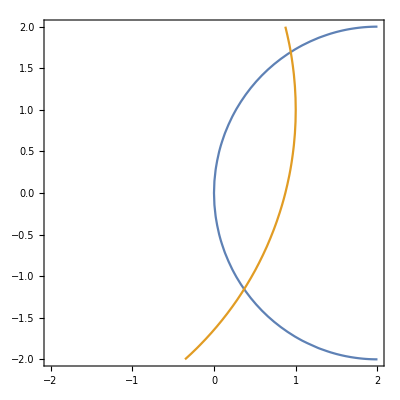

```mathematica
f[x_,y_]:=x^2-4 x+y^2
g[x_,y_]:=x^2+y^2+6 x-2 y-6
ContourPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2}]
```

```mathematica
FindRoot[{f[x,y],g[x,y]},{{x,1},{y,1}},WorkingPrecision->10]
```

{x→0.9390845572,y→1.695422786}

```mathematica
FindRoot[{f[x,y],g[x,y]},{{x,0},{y,-1}},WorkingPrecision->10]
```

{x→0.3686077505,y→-1.156961248}

```mathematica
(* -- Метод но Нютон за нелинейна система --- *)
f[x_,y_]:=x^2-4 x+y^2
g[x_,y_]:=x^2+y^2+6 x-2 y-6
Subscript[x, 0]=1;
Subscript[y, 0]=1;
For[n=0,n<5,n++,Subscript[X, 0]=({{Subscript[x, 0]}, {Subscript[y, 0]}});
F=({{f[Subscript[x, 0],Subscript[y, 0]]}, {g[Subscript[x, 0],Subscript[y, 0]]}});
Φ=({{D[f[x,y], x], D[f[x,y], y]}, {D[g[x,y], x], D[g[x,y], y]}})/.{x->Subscript[x, 0],y->Subscript[y, 0]};
Subscript[X, n]=Subscript[X, 0]-Inverse[Φ].F;
d=Norm[Subscript[X, n]-Subscript[X, 0]];
Print[Subscript["X",n]," = ",N[MatrixForm[Subscript[X, 0]]],
"    ",Subscript["F",n]," = ",N[MatrixForm[F]],
"    ",Subscript["Φ",n]," = ",N[MatrixForm[Φ]],
"    ",Subscript["Φ^-1",n]," = ",N[MatrixForm[Inverse[Φ]]],
"    d= ",N[d]];
Subscript[x, 0]=Subscript[X, n][[1,1]];
Subscript[y, 0]=Subscript[X, n][[2,1]]]
```

X_0 = (1.
2.)    F_0 = (-2.
0.)    Φ_0 = (-2. | 2.
8. | 0.)    (Φ^-1)_0 = (0. | 0.125
0.5 | 0.125)    d= 0.

X_1 = (1.
2.)    F_1 = (1.
1.)    Φ_1 = (-2. | 4.
8. | 2.)    (Φ^-1)_1 = (-0.0555556 | 0.111111
0.222222 | 0.0555556)    d= 0.283279

X_2 = (0.944444
1.72222)    F_2 = (0.0802469
0.0802469)    Φ_2 = (-2.11111 | 3.44444
7.88889 | 1.44444)    (Φ^-1)_2 = (-0.0477941 | 0.113971
0.261029 | 0.0698529)    d= 0.0270781

X_3 = (0.939134
1.69567)    F_3 = (0.000733225
0.000733225)    Φ_3 = (-2.12173 | 3.39134
7.87827 | 1.39134)    (Φ^-1)_3 = (-0.0468939 | 0.114302
0.26553 | 0.0715112)    d= 0.000252021

X_4 = (0.939085
1.69542)    F_4 = (6.35148×10^-8
6.35148×10^-8)    Φ_4 = (-2.12183 | 3.39085
7.87817 | 1.39085)    (Φ^-1)_4 = (-0.0468854 | 0.114305
0.265573 | 0.0715269)    d= 2.18348×10^-8